# SpectralRandomnessTest

Uses a discrete cosine transform–based method to test the randomness of a sequence of random reals.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&InexactNumberQ[#]&]]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"PValue"];
```

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&InexactNumberQ[#]&],"PValue"]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"PValue"];
```

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&InexactNumberQ[#]&],"TestStatistic"]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"TestStatistic"];
```

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"PValue"];
```

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"PValue"];
```

```mathematica
SpectralRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=KolmogorovSmirnovTest[Rest@FourierDCT@seq,Automatic,"TestStatistic"];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

SpectralRandomnessTest[sequence]

conducts a discrete cosine transform–based test to asses the randomness of either a sequence of zeros and ones of reals between zero and one.

SpectralRandomnessTest[sequence,"property"]

conducts a discrete cosine transform–based test to asses the randomness of either a sequence of zeros and ones of reals between zero and one and returns the associated property.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Properties include

"TestStatistic" | Returns the test statistic
"PValue" | Returns the p-value associated with the test

The test statistic is generated by comparing the discrete cosine transformed data with the normal distribution using the Kolmogorov–Smirnov test.

The test works for sequences of of random reals between 0 and 1 and sequences of only 0s and 1s

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a sequence of random reals and apply a run discrete cosine transform-based test:

```mathematica
sequence=RandomReal[{0,1},1000];
```

Visualize the sequence:

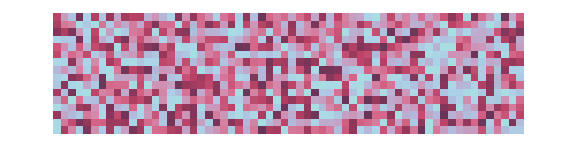

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
SpectralRandomnessTest[sequence,"TestStatistic"]
```

0.0186997

```mathematica
SpectralRandomnessTest[sequence,"PValue"]
```

0.559604

Generate a sequence of random integers and apply a run discrete cosine transform-based test:

```mathematica
sequence=RandomInteger[{0,1},1000];
```

Visualize the sequence:

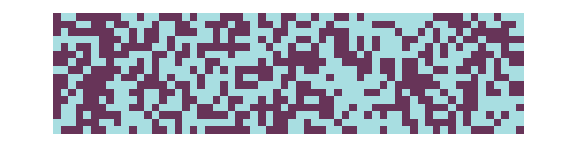

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
SpectralRandomnessTest[sequence,"TestStatistic"]
```

0.0129432

```mathematica
SpectralRandomnessTest[sequence,"PValue"]
```

0.967207

### Scope

Attempt to reject a non-random sequence:

```mathematica
subsequence=RandomInteger[{0,1},100];
```

```mathematica
sequence=Flatten[Table[subsequence,20]];
```

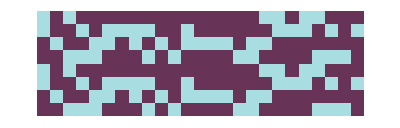

```mathematica
ArrayPlot[Partition[Take[sequence,200],25],]
```

```mathematica
SpectralRandomnessTest[sequence,"TestStatistic"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.298392

```mathematica
SpectralRandomnessTest[sequence,"PValue"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.

### Applications

Test to see if rule 30 is random according to the spectral test:

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

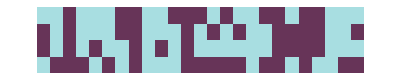

```mathematica
ArrayPlot[Partition[Take[rule30seq,100],25],]
```

```mathematica
SpectralRandomnessTest[rule30seq]
```

0.226717

### Properties and Relations

### Possible Issues

For non-random data, the Kolmogorov–Smirnov test, a part of the entire test, may return ties. Observing such ties is a strong indicator that the data is non–random:

```mathematica
subsequence=RandomInteger[{0,1},100];
```

```mathematica
sequence=Flatten[Table[subsequence,20]];
```

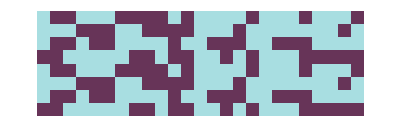

```mathematica
ArrayPlot[Partition[Take[sequence,200],25],]
```

```mathematica
SpectralRandomnessTest[sequence,"TestStatistic"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.277891

```mathematica
SpectralRandomnessTest[sequence,"PValue"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.

### Neat Examples

Visualize the sampling distribution of the test statistic:

```mathematica
samp=SpectralRandomnessTest[#,"TestStatistic"]&/@RandomReal[{0,1},{1000,1000}];
```

```mathematica
Histogram[samp,Automatic,"PDF"]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Emmy/Noah Blumenthal
noahb320@gmail.com
emmyb320@bu.edu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Randomness

Statistics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

DistributionFitTest

KolmogorovSmirnovTest

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

ChiSquareRandomnessTest

OPERM5RandomnessTest

RunLengthRandomnessTest

SerialRandomnessTest

RunCountRandomnessTest

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Knuth, Donald E. The Art of Computer Programing.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Wikipedia

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

## Author Notes

This test, as far as I am aware, is an original test.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.